90 points

# Plotting Curves

## Mario L Gutierrez

Six Problems each worth 20 points.

## Introduction to Plotting

Read S 4.1 4.2, R p116-137

Query Plot in the document center. You notice that it has 82 options many of which can be combined. This gives very fine control over the appearance of plots. We are going to cover what in my judgement are the 18 most important options. When you encounter an option you should query it. It is a good idea to go through all of the options at your leisure. Knowledge of most of them are necessary to be a Mathematica master.

We have already encountered the Plot command in its simplest form.

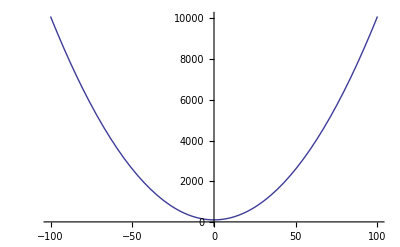

```mathematica
Plot[x^2+100,{x,-100,100}]
```

Notice that the axes intersect at (0,1000). Later we will see haw to control the axes-intersection.

```mathematica
Clear[x,y]
```

```mathematica
nd=(ⅇ^(-y^2))/(√(2π))
```

(ⅇ^(-y^2))/(√(2 π))

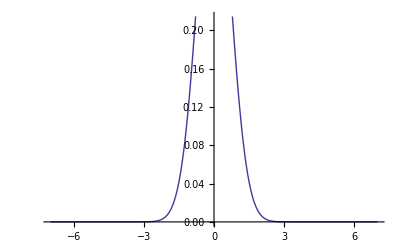

```mathematica
Plot[nd,{y,-7,7}]
```

#### PlotRange

Notice that Mathematica is cutiing of part of the graph along the y-axis. Mathematica tries to only show the most interesting parts of the plot. We can remedy this with the PlotRange option

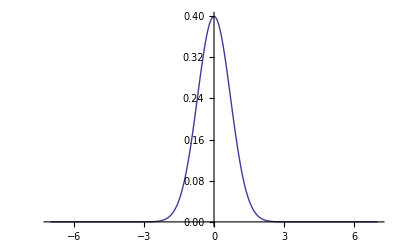

```mathematica
Plot[nd,{y,-7,7},PlotRange->All]
```

```mathematica
Clear[nd]
```

Read S 4.1 ex 3,

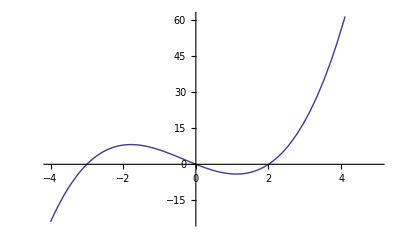

```mathematica
Plot[x(x-2)(x+3),{x,-4,5}]
```

Focusing on the local minimum

```mathematica
Plot[x(x-2)(x+3),{x,-2,5},PlotRange->{{.6,1.8},{-5,0}}]
```

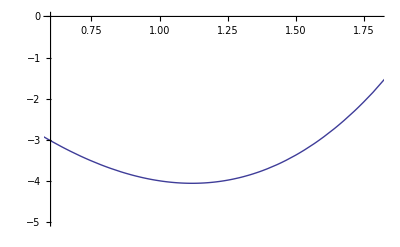

### AspectRatio

Query Read S exercise 7,8

When we plot a graph by hand we choose a pair of intersecting lines and then choose a unit on each line. There is no reason to choose the  length of these units to be the same. By default Mathematica chooses these lengths so that the graph will fit in a rectangle whose horizontal and vertical sides are in golden ratio that horizontal/veritcal=ϕ=(1+√5)/2. The ratio of vertical side to horizonal side can be changed by the option AspectRatio. The most used value of AspectRatio is Automatic. This has the effect of making the units on the axes the same length. As we saw in S ex8 the default AspectRatio deforms geometry. Here is another example

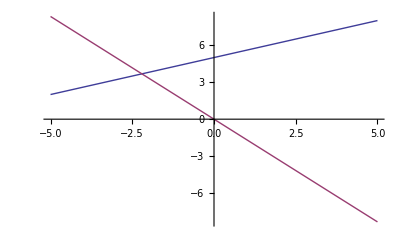

```mathematica
Plot[{3/5 z+5,-5/3 z},{z,-5,5}]
```

The slopes of these lines are negative reciprocal so they  should be perpindicular. the angle is deformed because the horizontal and vertical units are of different length.

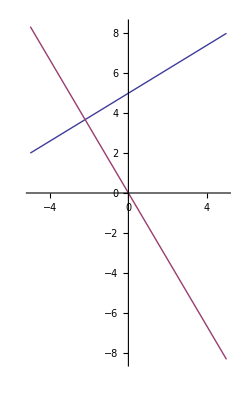

```mathematica
Plot[{3/5 z+5,-5/3 z},{z,-5,5},AspectRatio->Automatic]
```

So why not use AxisRatio->Automatic all the time. The reason is that we will often get unreadably norrow or wide graphs.

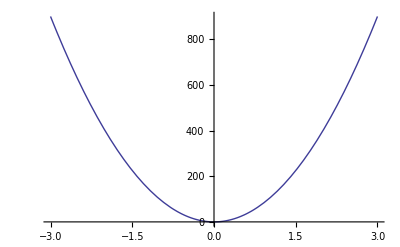

```mathematica
Plot[100 x^2,{x,-3,3}]
```

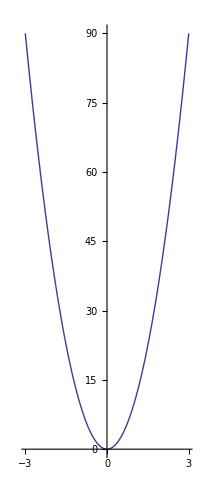

```mathematica
Plot[10 x^2,{x,-3,3},AspectRatio->Automatic]
```

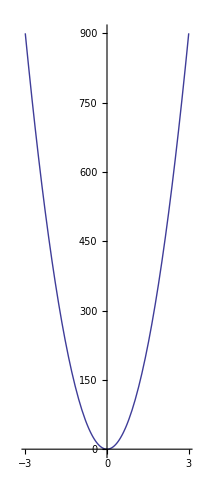

```mathematica
Plot[100 x^2,{x,-3,3},AspectRatio->Automatic]
```

The plot is so much taller than it is wide that all of its features vanish into the y-axis.

### PlotStyle

Read S. 98-100 pay particular attention to examples 10,11,12. PlotStyles can be combined

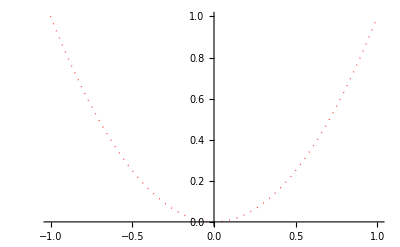

```mathematica
Plot[x^2,{x,-1,1},PlotStyle->{{Red,Dotted,Thick}}]
```

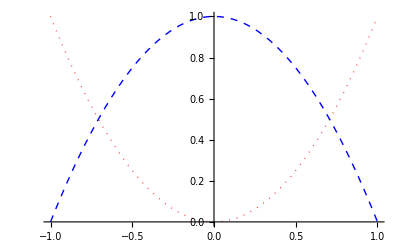

```mathematica
Plot[{x^2,1-x^2},{x,-1,1},PlotStyle->{{Red,Dotted,Thick},{Blue,Dashed}}]
```

#### ToolTip

Query Tooltip.. You won’t find it in S. but R and the document center have good explanations.

```mathematica
f[x_]:=Sin[x]
```

```mathematica
g[x_]:=x
```

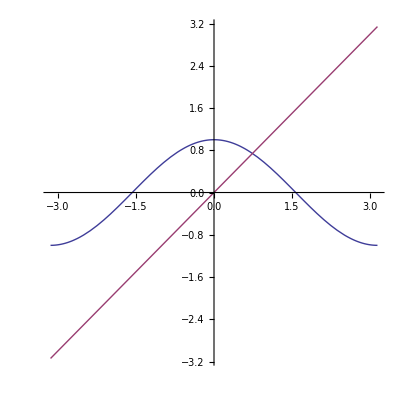

```mathematica
Plot[{Tooltip[Cos[x],"cosine"],Tooltip[x,"identity"]},{x,-π,π},AspectRatio->Automatic]
```

Now slide the mouse over each curve

#### Axes, Frame

Please Read S 104  Pay particular attention to  execise 18. and 19. Query Axes and Frame. The document center and R are also quite good for this query

#### AxesStyle

Query AxesStyle

#### AxesOrigin

Query AxesOrigin. Mathematica makes a choice on where to place the intersection of the origin. We can place this intersection wherever we like using the option AxesOrigin. Read S exercise 9..

Continuing the example we did under PlotRange:

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x(x-2)(x+3)
```

```mathematica
xcoord=x/.Solve[D[f[x],x]==0,x]
```

{1/3 (-1-√19),1/3 (-1+√19)}

```mathematica
N[1/3 (-1+√19)]
```

1.11963

```mathematica
N[f[1/3 (-1+√19)]]
```

-4.06067

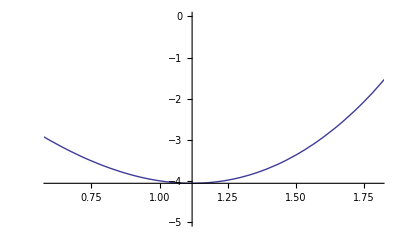

```mathematica
Plot[x(x-2)(x+3),{x,-2,5},PlotRange->{{.6,1.8},{-5,0}},AxesOrigin->{1/3 (-1+√19),f[1/3 (-1+√19)]}]
```

#### AxesLabel,PlotLabel

Query AxesLabel and PlotLabel. Look at S ex 15.

#### Ticks

Query Ticks and TicksStyle. You will need the document center for TicksStyle. Look at S exercise 20

#### Gridlines

Query Gridlines look at S. exercise 19

#### Exclusions

Query Exclusions. There is no reference in S. the document center is unclear and so is R. We give our own examples:Consider:

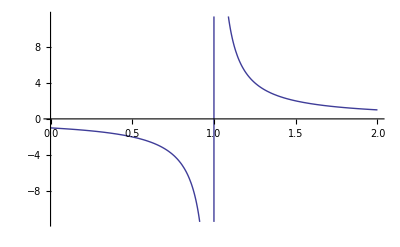

```mathematica
Plot[1/(x-1),{x,0,2}]
```

The vertical line is not an asymptote. Rather it is a plotting artifact coming from the fact the Mathematica is choosing points and connecting the by straight lines. In this case it is choosing points to the left and the right of 1 and connecting them by straight lines. We can remedy this by using the option Exclusions, where we can exclude to solutions to equations or list of equations

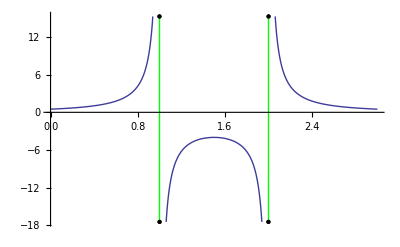

```mathematica
Plot[1/((x-1)(x-2)),{x,0,3}, Exclusions->{x==1,x==2},ExclusionsStyle->{Green,Dotted}]
```

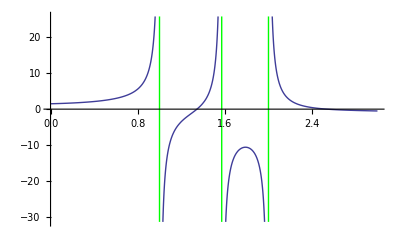

```mathematica
Plot[1/((x-1)(x-2))+Sec[x],{x,0,3}, Exclusions->{Denominator[1/((x-1)(x-2))]==0,Cos[x]==0},ExclusionsStyle->{Green}]
```

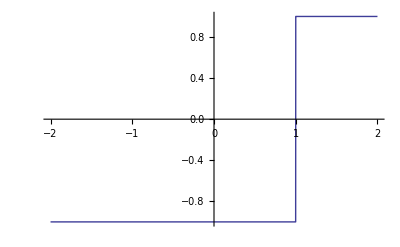

```mathematica
Plot[(x-1)/Abs[x-1],{x,-2,2}]
```

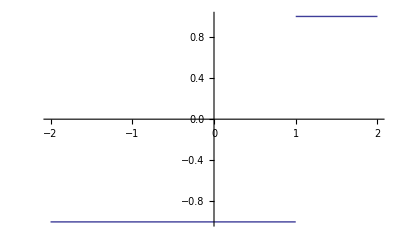

```mathematica
Plot[(x-1)/Abs[x-1],{x,-2,2},Exclusions->{1}]
```

#### Filling

Query Filling. This command is what you use to illustrate problems concerning the area between curves, Its syntax is rather complicated S 106-107 gives several examples. It gets a little complicated if you want to fill between two curves. This is case when you want to illustrate the area between two curves.

#### ImageSize

Query ImageSize. This command is used to determine how large the graphics will be.

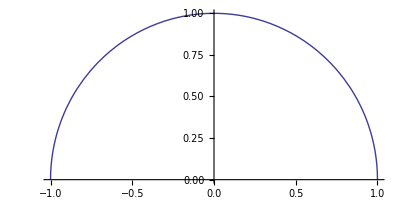

```mathematica
Plot[√(1-x^2),{x,-1,1},AspectRatio->Automatic]
```

```mathematica
Plot[√(1-x^2),{x,-1,1},AspectRatio->Automatic,ImageSize->100]
```

-Graphics-

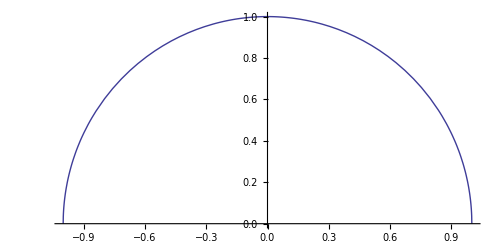

```mathematica
Plot[√(1-x^2),{x,-1,1},AspectRatio->Automatic,ImageSize->500]
```

#### Adaptive PlotPoints, MaxRecursion

Query PlotPoints and MaxRecursion. These options control the mechanics behind Mathematica’s adaptive plotting routines. I quote from a terrific book of sophisticated examples Mathematica in Action, Stan Wagon

“The general idea underlying the basic plotting algoritm is as follows. The function is evaluated at PlotPoints equally spaced points. If the angle between consecutive line segments is less that 5°, the algorithm is happy and moves on. If not it subdivides ( the maximum number of subdivisions is controlled by MaxRecursion) until the angle criterion is reached. “

Raising PlotPoints and MaxRecursion can smooth out “jaggies” . But this comes at the cost of the time it takes to plot. This becomes particularily important in two dimensional plots.

#### Working Precision

When Mathematica does the numerical computation of expressions to be plotted it works with machine (chip) precision. Sometimes raising the precision of calculations gives more accurate results. This is controlled with the option WorkingPrecision.

If we want to see the effect of working precision we quote an example from Mathematica in Action, Stan Wagon. I recommend this book because it gives lots of interesting, nontrivial examples of the use of Mathematica. First I use a command that gives the Maclauren (Taylor polynomial) of a function f(x)  to degree 200:

```mathematica
poly=Normal[Series[Cos[x],{x,0,200}]];
```

This is the Taylor polynomial of cos(x) around 0 to the term of degree 200 Analytically out to x=50 it is a very accurate approximation to cos(x). Let’s first try to plot it

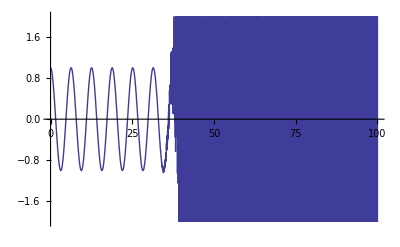

```mathematica
Plot[poly,{x,0,100},PlotRange->{-2,2}]
```

The reason why we get the square in the plot can be seen by looking at later terms in the polynomial:

```mathematica
poly[[-3;;-1]]
```

x^196/508012211086704676250273578534744855832729752494702698292997143104359057480013603705540137242115195719262628671043031667501252088161309228461647972823682280495348903461291560889483687823263915860291345617137392657194686983749887501702176113098676677779711031060019608283576803094698692188285748113739606947612227692134400000000000000000000000000000000000000000000000-x^198/19815524305648002601818171204326257846611456725808373449616646563928629396065410626138298593265945324225558093942704493222553838950820027765375040827960551033001579328411138624055200727234232302046524227142061137986535960488148111891395081467526982493475408477527124840709196781511817187496273890924527108598562553359394406400000000000000000000000000000000000000000000000+x^200/788657867364790503552363213932185062295135977687173263294742533244359449963403342920304284011984623904177212138919638830257642790242637105061926624952829931113462857270763317237396988943922445621451664240254033291864131227428294853277524242407573903240321257405579568660226031904170324062351700858796178922222789623703897374720000000000000000000000000000000000000000000000000

Something peculiar is going on because this Maclaurin polynomial should give a very accurate approximation of cos (x). The problem is that Plot is working to machine precision, and at machine precision there are severe rounding errors in evaluating poly. High powers easily introduce rounding errors.

Let’s up the precision (work in software precision)

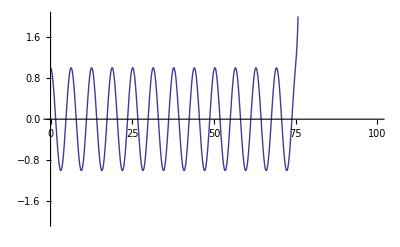

```mathematica
Plot[poly,{x,0,100},PlotRange->{-2,2},WorkingPrecision->100]
```

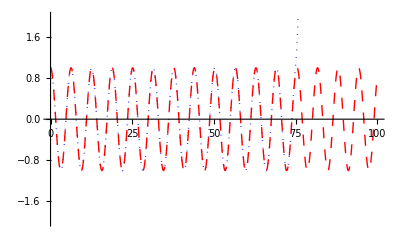

```mathematica
Plot[{poly,Cos[x]},{x,0,100},PlotRange->{-2,2},WorkingPrecision->60,PlotStyle->{{Dotted,Blue},{Red,Dashing[.02]}}]
```

We are doing much better. As always working with software precision takes longer.

### Interface issues

Make a plot and the left click on it. You will see a rectangle with four handles. Clicking on a handle and sliding will change the shape of the graphic. If you move to one of the lines (not a handle) and do this precisely enough that the cursor turns into a cross you can drag the graphic.

#### Problem 1

Let

```mathematica
xval=Union[Table[θ,{θ,0,2π,π/4}],Table[θ,{θ,0,2π,π/6}]]
```

{0,π/6,π/4,π/3,π/2,(2 π)/3,(3 π)/4,(5 π)/6,π,(7 π)/6,(5 π)/4,(4 π)/3,(3 π)/2,(5 π)/3,(7 π)/4,(11 π)/6,2 π}

Produce the plot

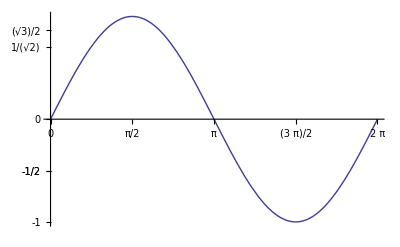

Hint: First produce the table of y values and then use the two tables you have as the input to Ticks and GridLines. Then click on the plot and place the cursor over the orange handle in the center and drag to expand the plot, so that the y-ticks don’t overlap.

```mathematica
f[x_]:=Sin[x]
```

```mathematica
xval=Union[Table[θ,{θ,0,2π,π/4}],Table[θ,{θ,0,2π,π/6}]]
```

{0,π/6,π/4,π/3,π/2,(2 π)/3,(3 π)/4,(5 π)/6,π,(7 π)/6,(5 π)/4,(4 π)/3,(3 π)/2,(5 π)/3,(7 π)/4,(11 π)/6,2 π}

```mathematica
yval=f[xval]
```

{0,1/2,1/(√2),(√3)/2,1,(√3)/2,1/(√2),1/2,0,-1/2,-1/(√2),-(√3)/2,-1,-(√3)/2,-1/(√2),-1/2,0}

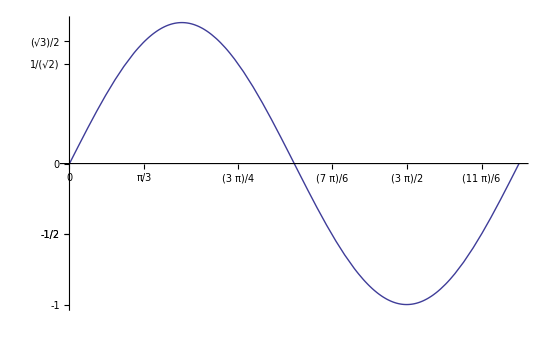

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{xval,yval},TicksStyle->Directive[Black,14],GridLines->{xval,yval},GridLinesStyle->Directive[Green],ImageSize->550]
```

20 points

Query the commands TrigExpand,TrigReduce and TrigFactor.

To zoom in on a plot near a number is to use smaller and smaller plot domains around the number. As an example suppose we want to know the first five decimal places of the solution to x^5+x+1=0. We say the solution since a polynomial of odd degree has a real solution and x^5+x+1 is increasing. Later when we see how to use the NSolve command we will do this non-geometically but using Plot we find:

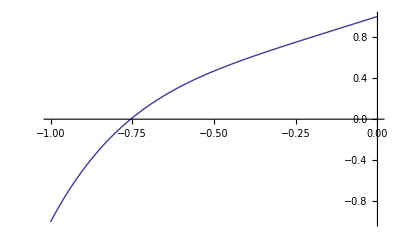

```mathematica
Plot[x^5+x+1,{x,-1,0}]
```

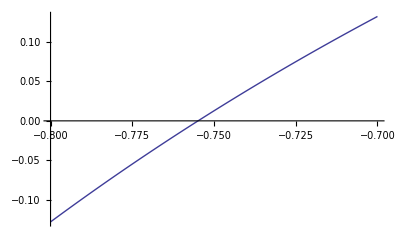

```mathematica
Plot[x^5+x+1,{x,-.8,-.7}]
```

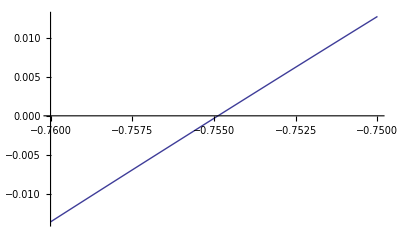

```mathematica
Plot[x^5+x+1,{x,-.76,-.75}]
```

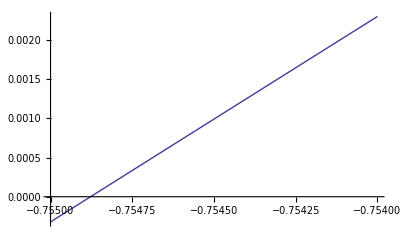

```mathematica
Plot[x^5+x+1,{x,-.755,-.754}]
```

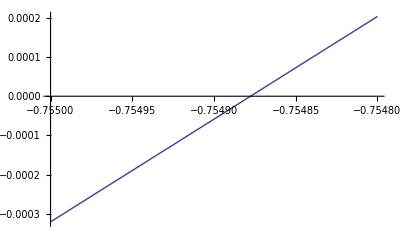

```mathematica
Plot[x^5+x+1,{x,-.755,-.7548}]
```

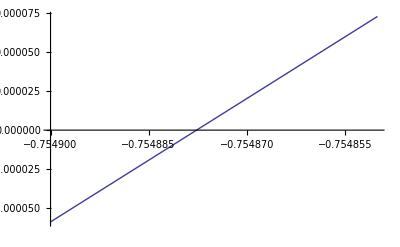

```mathematica
Plot[x^5+x+1,{x,-.75490,-.75485}]
```

Rounding we get the solution is -.75488

```mathematica
x/.NSolve[x^5+x+1==0,x,Reals]
```

{-0.754878}

### Problem 2

Show that there are 11 solutions to the equation 2cos^2(2x)-Sin(x/2)=1 in the interval [0,3π]. First look at the plot  of  expr where expr=2 Cos[2x]^2-Sin[x/2]-1 . Lots of the solutions will be clear visually but there is one place where it is not clear the graph is intersecting the axis or if so how many times. Zoom in on that place.  Guess at the solution. Check the  guess, and then confirm there is only one solution in some interval around the place using calculus (second derivative test).

```mathematica
exp=2 Cos[2x]^2-Sin[x/2]-1;
```

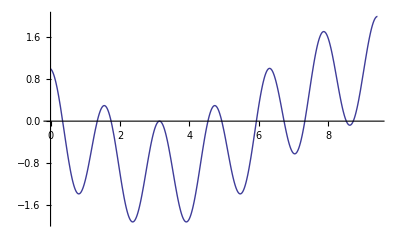

```mathematica
Plot[exp,{x,0,3π}]
```

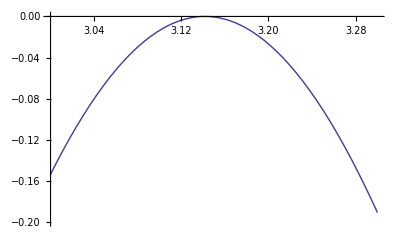

```mathematica
Plot[exp,{x,3,3.3},PlotRange->{-.2,0}]
```

After zooming in my guess is that the one solution for our function on this interval is π.
Now using calculus:

```mathematica
exp /.x->π
```

0

```mathematica
D[exp,{x,1}]/.x->π
```

0

```mathematica
D[exp,{x,2}]/.x->π
```

-63/4

Since our first derivative is equal to zero and the second derivative at x=π is negative (downward concavity), that means that we have a local maximum at that point. Also at this point the function is equal to zero (exp /.x→π = 0), which means that our critical point is indeed a solution to the equation.

20 points. But why does local max guarantee that there is exactly on solution in some neighborhood of π

## Curves In R^2

Curves in R^2 can be described in three ways:

Plots of Functions , Example f(x)=Sin[x+100Sin(x)), Mathematica command Plot

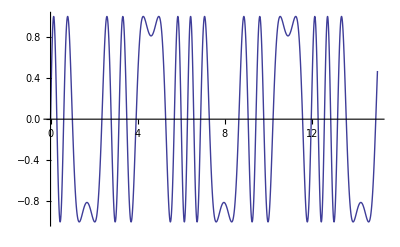

```mathematica
Plot[Sin[x+10Sin[x]],{x,0,15}]
```

Implicitly Defined Curves, Example u^3+v^3=u v. Query Mathematica command ContourPlot

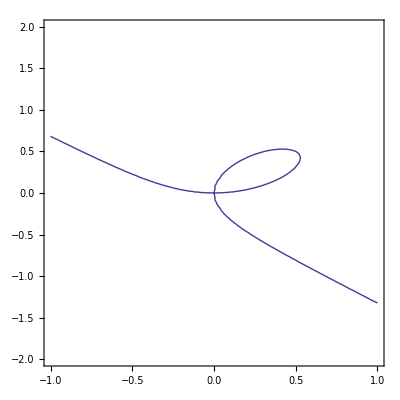

```mathematica
ContourPlot[u^3+v^3==u v,{u,-1,1},{v,-2,2}]
```

Parametrically Defined Curves, Example x(t)=3cos(t)+8Cos(3/8 t),y(t)=3Sin(t)-8Sin(3/8 t) t goes from 0 to 10π. Query Mathematica command ParametricPlot.

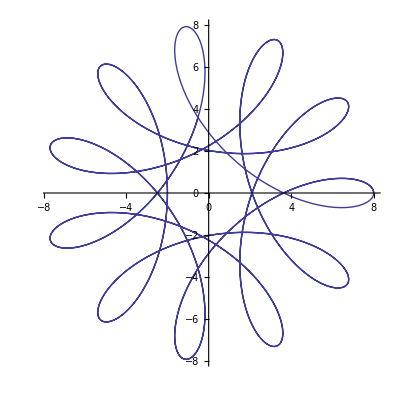

```mathematica
ParametricPlot[{3Cos[t]+5Cos[3/8 t],3Sin[t]-5Sin[3/8 t]},{t,0,30π}]
```

## ContourPlot

Consider an equation in two variables, and think of a real valued solution to the equation as a point in the plane. The locus of the equation is the set of the solutions of the equation. Consider the equation x^2+y^2+2x y==1. We look at the locus of this equation in a rectangle and we get a rotated hyperbola.

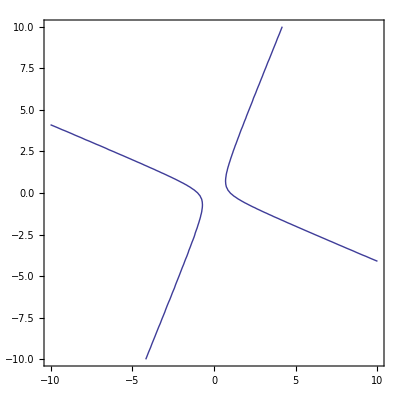

Clearly this is not the graph of a function. We say however that the equation gives an implicit function. If we want to be precise the functions we have encountered up till now are explicit functions. By the way every explicit function is an implicit function. The explicit  definition y=f(x) is equivalent to the equation f(x)-y=0.

Query the command ContourPlot. For plotting the locus of an equation in two variables its syntax is ContourPlot[equation,{x,x_min,x_max},{y,y_min,y_max}]. We also have the syntax ContourPlot[{eq1,eq2,⋯,eqn},{x,xmin,xmax},{y,ymin,ymax}].

Later when we get to three dimensional graphs we will discuss the full potential of ContourPlot (S 5.2)

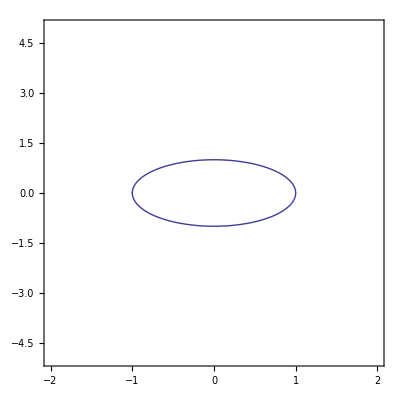

```mathematica
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-5,5}]
```

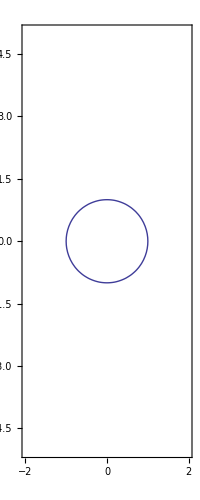

```mathematica
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-5,5},AspectRatio->Automatic]
```

The domain specification which comes first determines which variable runs horizontally. The second determines the variable that runs vertically

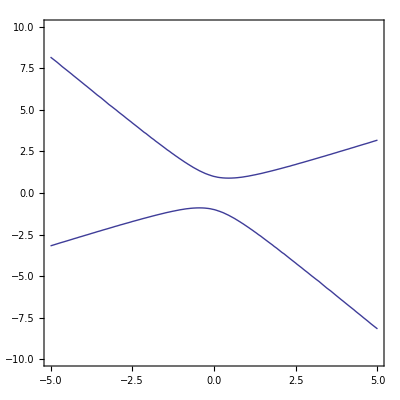

```mathematica
ContourPlot[x^2+y^2+x y==1,{y,-5,5},{x,-10,10}]
```

```mathematica
ContourPlot[{x^2-y^2+x y==1,x^2/5^2+y^2/2^2==1},{y,-5,5},{x,-6,6}]
```

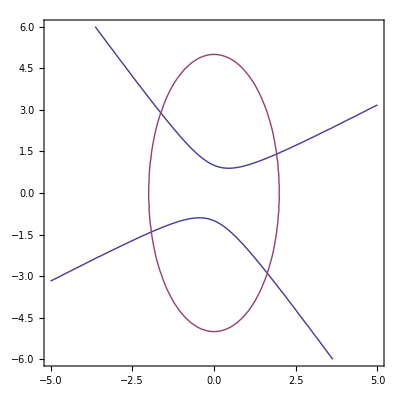

An idiosyncracy of ContourPlot: If we name an equation

```mathematica
hyp=x^2-y^2+x y==1
```

```mathematica
x^2+x y-y^2==1
```

```mathematica
ContourPlot[hyp, {y, -5, 5}, {x, -10, 10}]
```

-Graphics-

We have to wrap the name in Evaluate.

```mathematica
ContourPlot[Evaluate[hyp], {y, -5, 5}, {x, -10, 10}]
```

-Graphics-

The same goes for list of names. We have to wrap the list.

```mathematica
circ=x^2+y^2==3
```

```mathematica
x^2+y^2==3
```

```mathematica
ContourPlot[{hyp, circ}, {y, -5, 5}, {x, -10, 10}]
```

```mathematica
ContourPlot[Evaluate[{hyp, circ}], {y, -5, 5}, {x, -10, 10}]
```

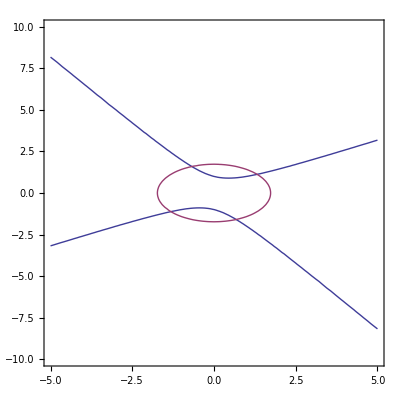

```mathematica
ContourPlot[Evaluate[{hyp, circ}], {y, -5, 5}, {x, -10, 10}, AspectRatio -> Automatic]
```

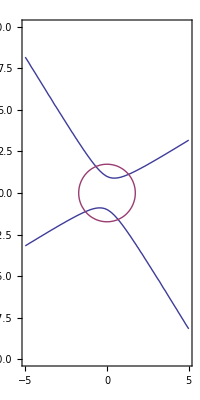

The next problem is a slight variant of Stewart’s calculus book page 217.

### Problem 3

a: Consider the function

```mathematica
f[c_]:=y^2-2 x^2(x+3)==c((y+1)^2(y+9)-x^2)
```

Observe that f takes on equations as its values.

How many points of intersection are there between the plots of f[1] and f[2]. You may need to zoom in on a rectangle in the center to see all of the intersection points.

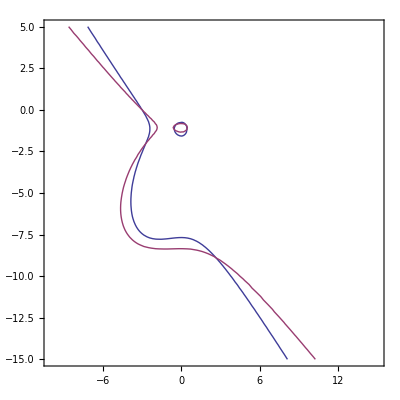

```mathematica
ContourPlot[Evaluate[{f[1],f[2]}],{x,-10,15},{y,-15,5}]
```

Now we zoom in in order to see all the intersection points

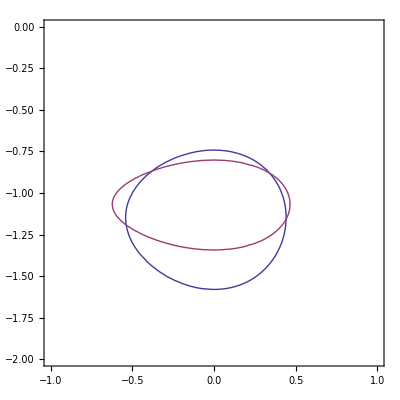

```mathematica
ContourPlot[Evaluate[{f[1],f[2]}],{x,-1,1},{y,-2,0}]
```

There appears to be 7 intersection points.

b: Now look at the intersection of the four curves f(-1),f(0),f(1),f(ⅇ),f(-π)

```mathematica
f[-1]
f[0]
f[1]
f[ⅇ]
f[-π]
```

-2 x^2 (3+x)+y^2==x^2-(1+y)^2 (9+y)

-2 x^2 (3+x)+y^2==0

-2 x^2 (3+x)+y^2==-x^2+(1+y)^2 (9+y)

-2 x^2 (3+x)+y^2==ⅇ (-x^2+(1+y)^2 (9+y))

-2 x^2 (3+x)+y^2==-π (-x^2+(1+y)^2 (9+y))

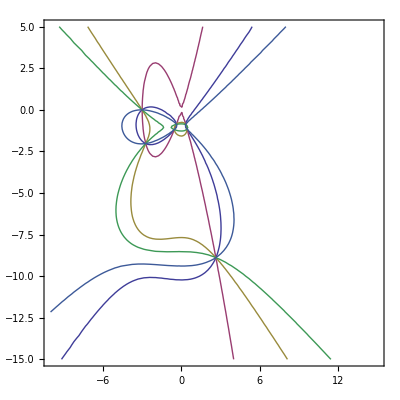

```mathematica
ContourPlot[Evaluate[{f[-1],f[0],f[1],f[ⅇ],f[-π]}],{x,-10,15},{y,-15,5}]
```

Once again we have to zoom in..

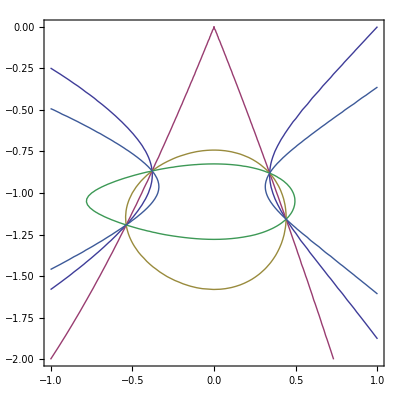

```mathematica
ContourPlot[Evaluate[{f[-1],f[0],f[1],f[ⅇ],f[-π]}],{x,-1,1},{y,-2,0}]
```

There also appears to be 7 intersection points for the 5 values of f[c_] shown above.

c: Now make a conjecture about the intersection of the plots of any finite list {f[c_1],f[c_2]…f[c_n]}

Based on the above observations, we may conclude that the intersection plots of any finite list {f[c1], f[c2],..., f[cn]} seem to always have the same number of intersection points.  For the defined function above, we will always have 7 intersection points in any finite list. In addition, it seems like these intersection points are exactly the same for our list of functions {f[c1], f[c2],..., f[cn]}.

20 points

## Parametrized Curves

Read S 111-112, R 5.2.1 and query ParametricPlot. Be sure to pay attention to the second line of the definition which allows you to plot several parametric curves at once. Looking at details and options you will see that Plot and ParametricPlot share many of the same options

### The cycloid

Take a circle and roll it along a horizontal line. A fixed point on the circle traces out a curve which is called the cycloid.

The cycloid is dealt with in the article cycloid. I don’t expect you to be able to read the whole thing.

Here is the parametrization of the cycloid, when the circle has radius a:

x=a(t-Sin[t]),y=a(1-Cos[t])

Since a is a radius we must have 0<a.

```mathematica
x[t_]:=a(t- Sin[t])
```

```mathematica
y[t_]:=a(1-Cos[t])
```

We plot in the special case a=1:

```mathematica
a=1
```

1

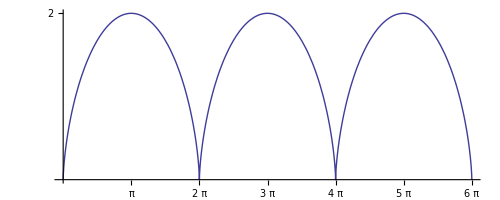

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,6π},Ticks->{Table[j π,{j,1,6}],{2}}]
```

```mathematica
Clear[a]
```

Clearly the cycloid is the graph of a function. That is there is some function f such that y=f(x). Unfortunately it is not possible to write y as a formula in x in terms of the classical functions of Mathematics

We want to find the area of one hump of the cycloid.As t goes from 0 to 2π we have x goes from 0 to 2aπ. By definition we have

area=∫_(x=0)^(x=2a π) f(x)ⅆx

We make a change of variable and we have

area=∫_(t=0)^(t=2π) y(t)x'(t)ⅆt

```mathematica
Integrate[y[t]x'[t],{t,0,2π}]
```

3 a^2 π

Recall that the arc-length of a parametrized curve as t goes from a to b is:

∫_a^b √(x'(t)^2+y'(t))ⅆt

For the cycloid we have

```mathematica
∫_0^(2π) √(x'[t]^2+y'[t]^2)ⅆt
```

8 √(a^2)

With the geometric restriction that 0<a we have

length=8a

## Fun With circles I: Hypotrochoids and Epitrochoids

Read Hypotrochoid and Epitrochoid. The cases where h=b are called the hypocycloid and the epicycloid respectively

One of the things that should be noted is that for a/b rational  ithe periods of the epitrochoid and hypotrochoid are 2π Denominator[a/b]

### Problem 4 Parametrizations

#### a: hypotrochoid

Define a Mathematica  function hypotrochoid[a_,b_,h_,t]_  which yieds a pair of expressions that are the x-coordinates and y-coordinates of the parametrization of the hypotrochoid

```mathematica
hypotrochoid[a_,b_,h_,t_]:=GridBox[{{(a-b)*Cos[t]+h Cos[(a-b)/b t]},{(a-b) Sin[t]-h Sin[(a-b)/b  t]}}]//DisplayForm
```

Example:

```mathematica
hypotrochoid[3,4,5,7]
```

5 Cos[7/4]-Cos[7]
5 Sin[7/4]-Sin[7]

10 points. This is much to complicated syntax, and it doesn’t really give a pair of parametrizations but rather a display of these parametrizations. If you try ParametricPlot on your functions

```mathematica
ParametricPlot[hypotrochoid[1,1/4/4,1/4,t],{t,0,2π}]
```

-Graphics-

You get an empty plot!

Professor, I used Gridbox on the syntax just because I’m being asked to display a pair of expressions. If I wanted to test it with a parametric plot I would’ve used instead

```mathematica
hypotrochoid1[a_,b_,h_,t_]:={{(a-b)*Cos[t]+h Cos[(a-b)/b t]},{(a-b) Sin[t]-h Sin[(a-b)/b  t]}}
```

Example:

```mathematica
hypotrochoid1[3,4,5,7]
```

{{5 Cos[7/4]-Cos[7]},{5 Sin[7/4]-Sin[7]}}

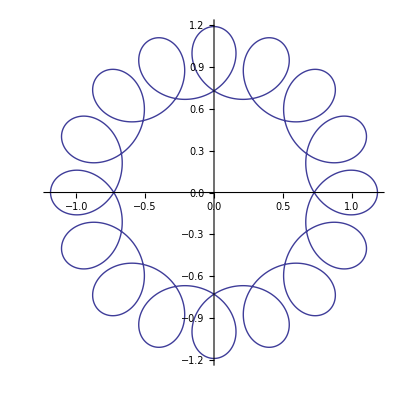

```mathematica
ParametricPlot[hypotrochoid1[1,1/4/4,1/4,t],{t,0,2π}]
```

#### b: Epitrochoid

Repeat a for the epitrochoid gettting the  function epitrochoid[a_,b_,h_,t_]

```mathematica
epitrochoid[a_,b_,h_,t_]:=GridBox[{{(a+b)*Cos[t]-h Cos[(a+b)/b t]},{(a+b) Sin[t]-h Sin[(a+b)/b  t]}}]//DisplayForm
```

Example:

```mathematica
epitrochoid[2,4,3,8]
```

6 Cos[8]-3 Cos[12]
6 Sin[8]-3 Sin[12]

5 points

Here I would’ve done the same as in 4a).

### Problem 5 The Curves

#### a Hypotrochoid

Define a function  spirohypo[a_,b_,h_] which gives the plot of the hypotrochoid, and the fixed circle. Be particularly careful of the parameter domain in light of the period of the hypocyclod.

```mathematica
x[a_,b_,h_]:=(a-b) Cos[t]+h Cos[((a-b)/b) t]
y[a_,b_,h_]:=(a-b) Sin[t]-h Sin[((a-b)/b) t]
```

```mathematica
spirohypo[a_,b_,h_]:= ParametricPlot[{{x[a,b,h],y[a,b,h]},{Cos[t],Sin[t]}},{t,0,2 Numerator[b] π},PlotRange->Full]
```

```mathematica
SetOptions[ParametricPlot,Ticks->None];
sp1=spirohypo[1,1/13 π^ⅇ,1/13 ⅇ^π];
sp2=spirohypo[1,1/12 π^ⅇ,1/15 π^ⅇ];
sp3=spirohypo[ⅇ,1/4 π^20 ,1/4 π^(1/3)];
sp4=spirohypo[1,(π/ⅇ)/16,(ⅇ/π)^3];
```

The parameter domain only works for a,b rational. Also re-look at what I said about the period

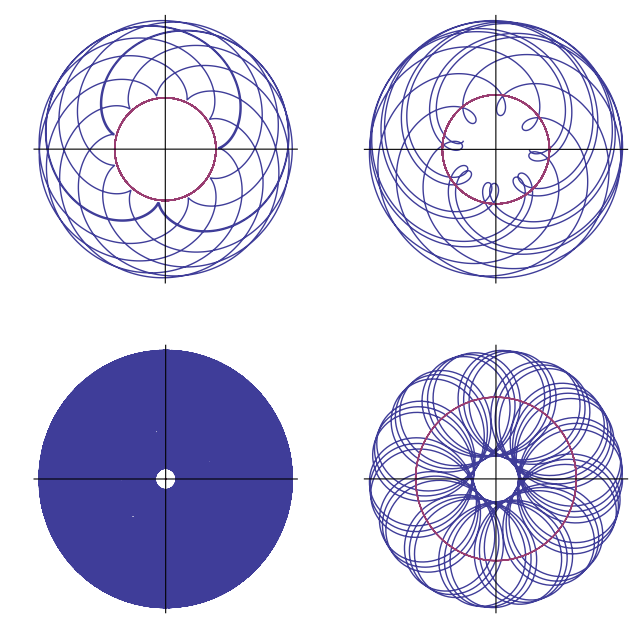

```mathematica
GraphicsGrid[{{sp1,sp2},{sp3,sp4}},ImageSize->640]
```

Here are some tests to make sure you got 5a right:  Then you should play with spirohypo and examine the variey of functions that you can produce. Show me a couple that you think are particularily pretty

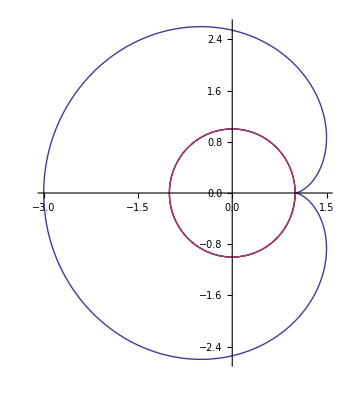

```mathematica
spirohypo[1,2,2]
```

A cardioid

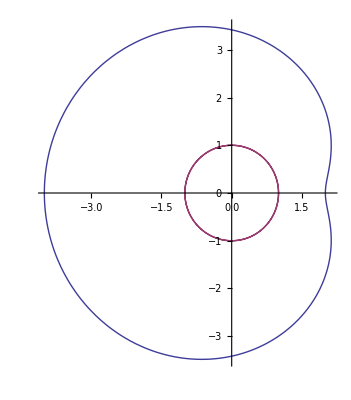

```mathematica
spirohypo[1,2,3]
```

A limniscate.

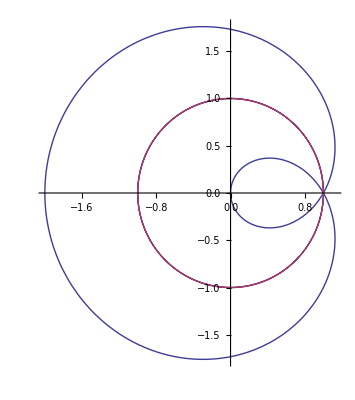

```mathematica
spirohypo[1,2,1]
```

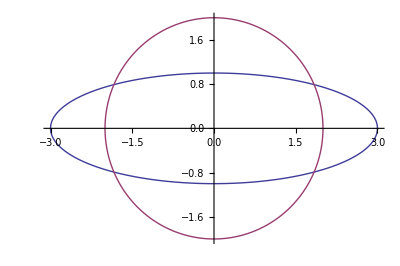

```mathematica
spirohypo[2,1,2]
```

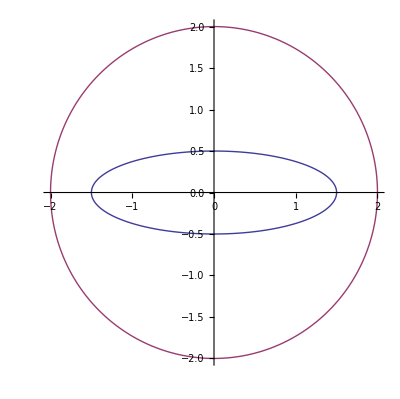

```mathematica
spirohypo[2,1,1/2]
```

Unusual parametrizations of the ellipse.

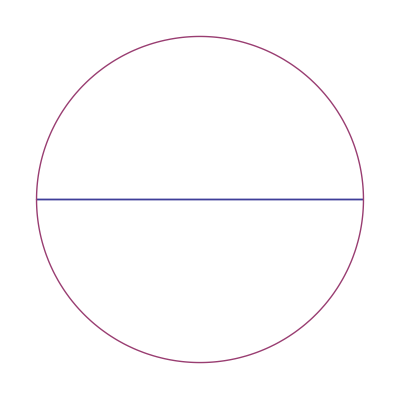

```mathematica
ParametricPlot[{hypotrochoid[2,1,1,t],{2Cos[t],2Sin[t]}},{t,0,2π},Axes->None]
```

A degenerate ellipse. A very special case where circular motion is being converted to linear motion. This actually used in the design of machines.

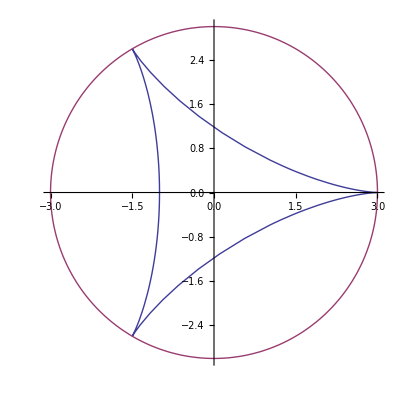

```mathematica
spirohypo[3,1,1]
```

A deltoid

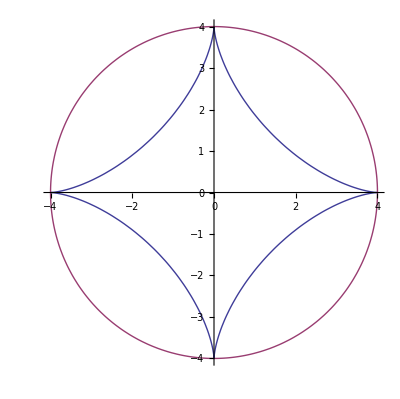

```mathematica
spirohypo[1,1/4,1/4]
```

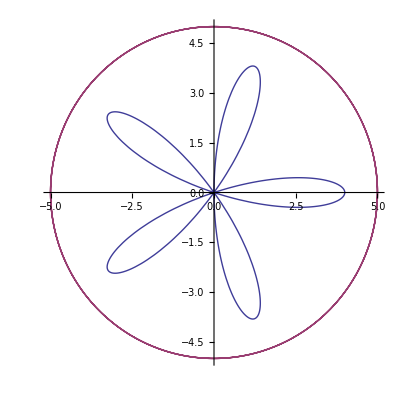

```mathematica
spirohypo[5,3,2]
```

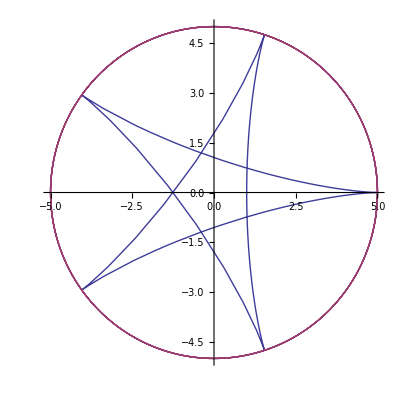

```mathematica
spirohypo[5,3,3]
```

h=b so we have a hypocycloid

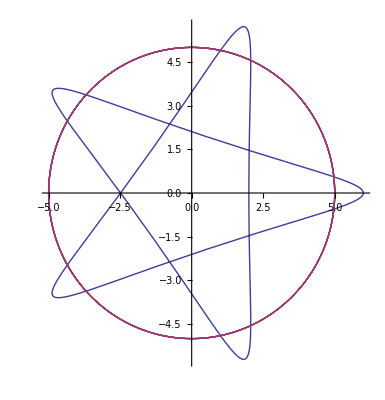

```mathematica
spirohypo[5,3,4]
```

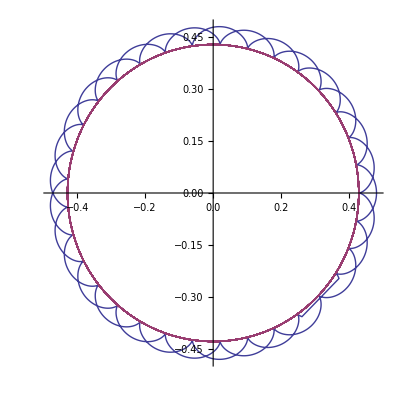

```mathematica
spirohypo[3/7,5/11,5/11]
```

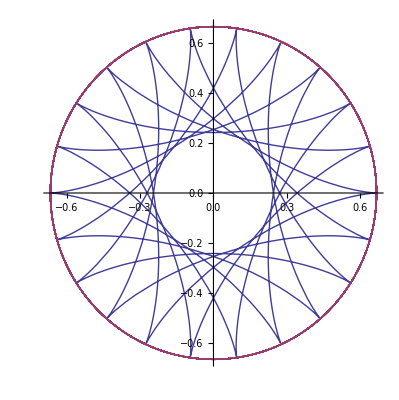

```mathematica
spirohypo[2/3,5/11,5/11]
```

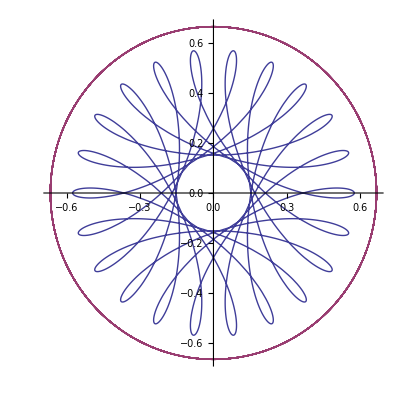

```mathematica
spirohypo[2/3,5/11,4/11]
```

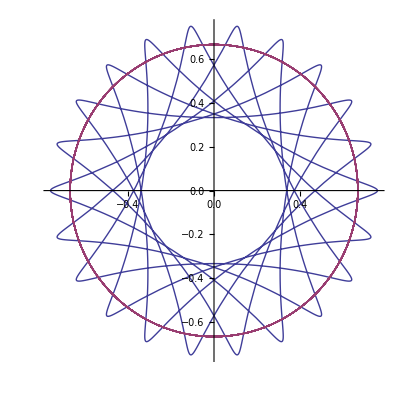

```mathematica
spirohypo[2/3,5/11,6/11]
```

#### b Epitrochoid

As in a define the function spiroepi[a_b_,h_]

```mathematica
x[a_,b_,h_]:=(a+b) Cos[t]-h Cos[((a+b)/b) t]
y[a_,b_,h_]:=(a+b) Sin[t]-h Sin[((a+b)/b) t]
```

```mathematica
spiroepi[a_,b_,h_]:=ParametricPlot[{{x[a,b,h],y[a,b,h]},{Cos[t],Sin[t]}},{t,0,2 Numerator[b] π},PlotRange->Full]
```

```mathematica
SetOptions[ParametricPlot,Ticks->None];
spep1=spiroepi[1,3/4,ⅇ];
spep2=spiroepi[1,π^ⅇ/ⅇ^π, (4 GoldenRatio)/7];
spep3=spiroepi[1,3/4,1/13 ⅇ^π];
spep4=spiroepi[1,GoldenRatio/(4π),1/13 ⅇ^π];
```

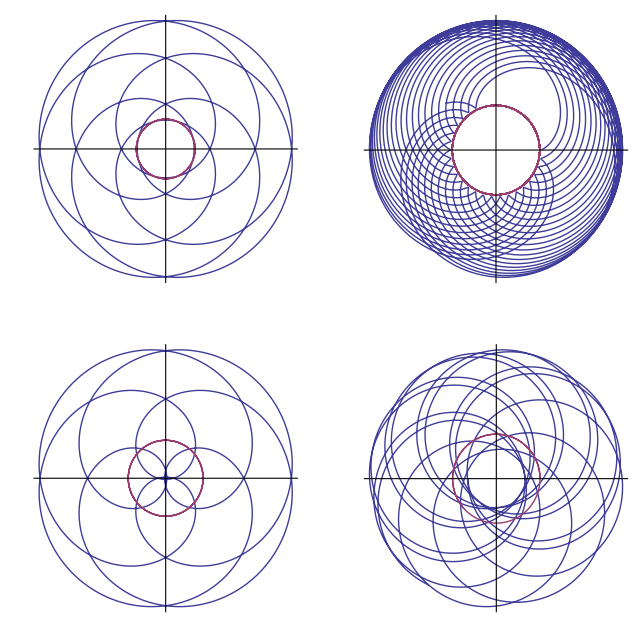

```mathematica
GraphicsGrid[{{spep1,spep2},{spep3,spep4}},ImageSize->640]
```

Here are some tests to make sure you got 4b and 5b right. You should run through them. Also on your scatch paper you might play with the spirohypo and spiroepi. In your answers you might show me a couple of curves you find particularily pretty. These curves are named after the  toy the Spirograph.

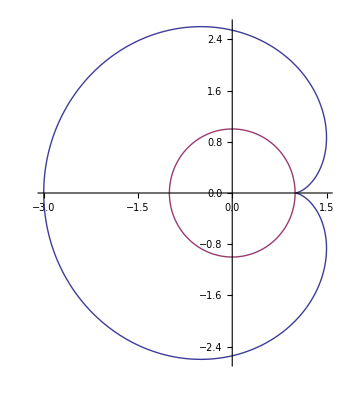

```mathematica
spiroepi[1,1,1]
```

We have already seen the cardioid presented as a hypocycloid, here it is as an epicycloid.

The two other cases of the limaçon:

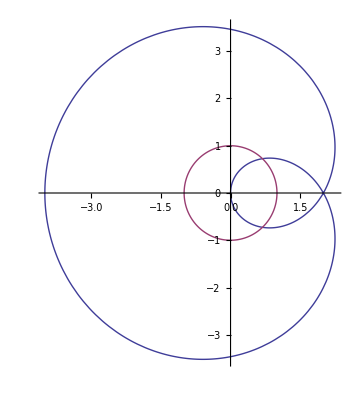

```mathematica
spiroepi[1,1,2]
```

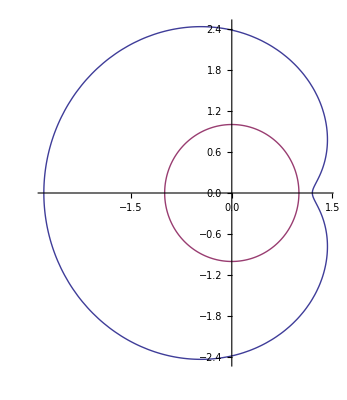

```mathematica
spiroepi[1,1,4/5]
```

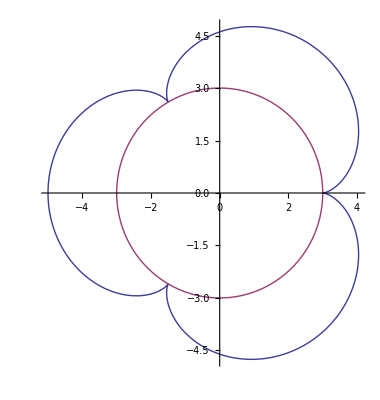

```mathematica
spiroepi[3,1,1]
```

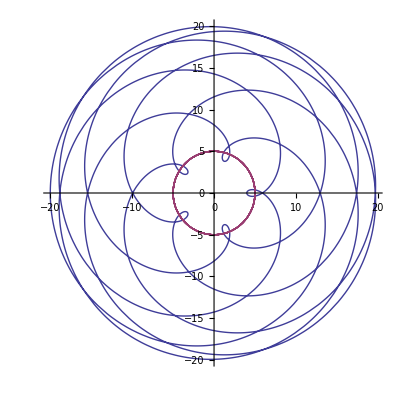

```mathematica
spiroepi[5,7,8]
```

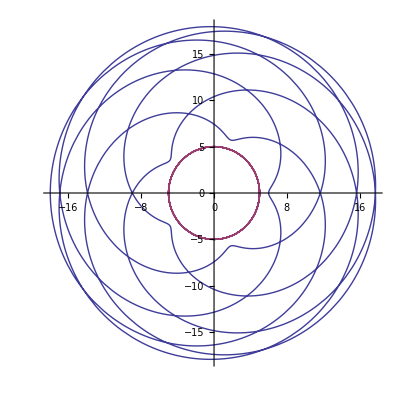

```mathematica
spiroepi[5,7,6]
```

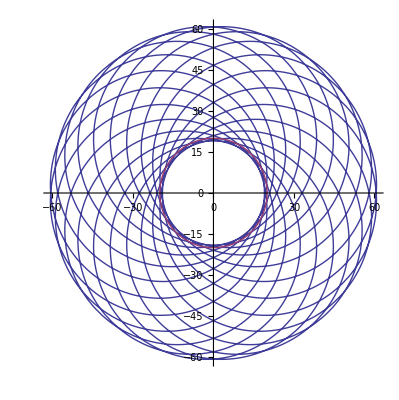

```mathematica
spiroepi[20,1,40]
```

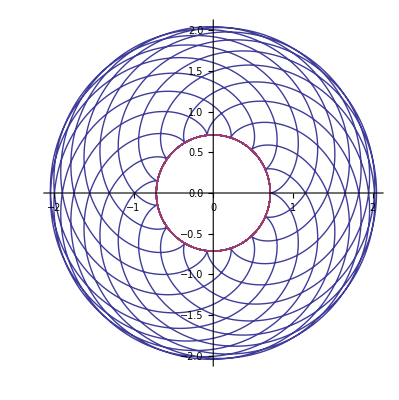

```mathematica
spiroepi[5/7,2/3,2/3]
```

The curves we have investigated are special cases of roullettes. This word is being used in its mathematical sense, rather than its Monte Carlo sense

5 points

#### Problem 6 The astroid

We are going to find the area and arc-length of the astroid much as we did that of the cycloid.

Recall the parametrization of the astroid

```mathematica
hypotrochoid[a,1/4 a,1/4 a,t]
```

{3/4 a Cos[t]+1/4 a Cos[3 t],3/4 a Sin[t]-1/4 a Sin[3 t]}

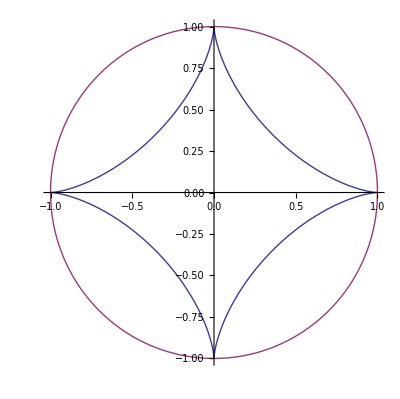

```mathematica
spirohypo[1,1/4,1/4]
```

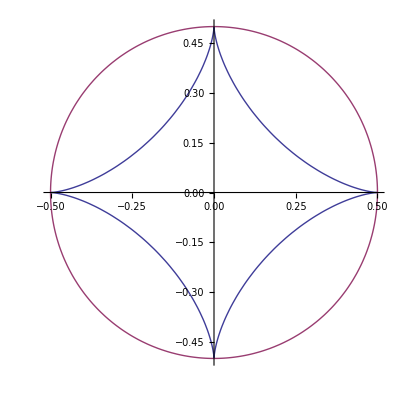

```mathematica
spirohypo[1/2,1/8,1/8]
```

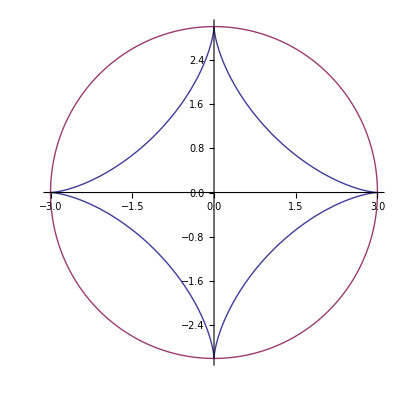

```mathematica
spirohypo[3,3/4,3/4]
```

The number a is the radius of the astroid it is also the radius of the enclosing circle

##### a: The parametrizing functions

Get the paparametrizing functions x[t_] and y[t_] of the astroid of radius a.

```mathematica
x[a_,t_]:=a Cos[t]^3
y[a_,t_]:=a Sin[t]^3
```

Where did you get this parametrization?

##### b: The area and the arc-length of the astroid

Like the ellipse clearly for the top half of the astroid y is a function f(x) of x. To find the area we need to compute

2∫_(x=-a)^(x=a) yⅆx

What is the first t such that x(t)=-a. What is the first t such that t=a, as x runs from -a to a what does t run from 2

Answer?

Now  as with the cycloid use a change of variables to evaluate  the area of the astroid

```mathematica
x[a_,b_,h_]:=(a-b) Cos[t]+h Cos[((a-b)/b) t]
y[a_,b_,h_]:=(a-b) Sin[t]-h Sin[((a-b)/b) t]
spirohypo[a_,b_,h_]:= ParametricPlot[{{x[a,b,h],y[a,b,h]},{Cos[t],Sin[t]}},{t,0,2 Numerator[b] π},PlotRange->Full]
```

```mathematica
spirohypo[1,1/4,1/4]
```

-Graphics-

```mathematica
x=x[1,1/4,1/4];
dx=D[x,t];
y=y[1,1/4,1/4];
dy=D[y,t];
Area=Integrate[Abs[y dx],{t,0,2 π}]
```

(3 π)/8

Evaluate the arc-length of the astroid

```mathematica
Integrate[√(dx^2+dy^2),{t,0,2 π}]
```

6

20 points. But see answers for the area of the general astroid of radius a.